### Set options here so we don’t need to include them in every function call

It’s possible to put these in a configuration file as well

```mathematica
SetOptions[FourierTransform,FourierParameters->{0,-1}]
```

{Assumptions:>$Assumptions,FourierParameters→{0,-1},GenerateConditions→False}

```mathematica
SetOptions[InverseFourierTransform,FourierParameters->{0,-1}]
```

{Assumptions:>$Assumptions,FourierParameters→{0,-1},GenerateConditions→False}

## Wide f(x) <----> narrow f̃(k)

```mathematica
Subscript[f, b_][x_]=Exp[-(x/b)^2]
```

ⅇ^(-x^2/b^2)

```mathematica
Subscript[f̃, b_][k_]=FourierTransform[Subscript[f, b][x],x,k,Assumptions->{b>0}]
```

(b ⅇ^(-1/4 b^2 k^2))/(√2)

```mathematica
FTPlot=Plot[{Subscript[f, 1/2][x],Subscript[f, 1][x],Subscript[f, 2][x]},{x,-4,4},PlotStyle->{Black,Blue,Red},PlotLegends->{"b=1/2", "b=1", "b=2"},FrameLabel->{"x","f(x)"}];
```

```mathematica
IFTPlot=Plot[{Subscript[f̃, 1/2][k],Subscript[f̃, 1][k],Subscript[f̃, 2][k]},{k,-4,4},PlotStyle->{Black,Blue,Red},PlotLegends->{"b=1/2", "b=1", "b=2"},FrameLabel->{"k","f̃(x)"}];
```

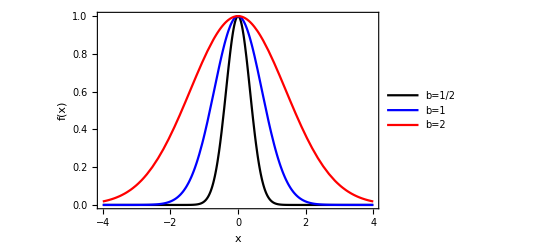

```mathematica
FTPlot
```

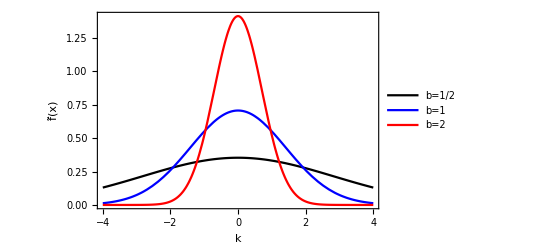

```mathematica
IFTPlot
```

```mathematica
Manipulate[
Plot[{Subscript[f, b][x],Subscript[f̃, b][x]},{x,-4,4},PlotStyle->{Darker[Green],Purple},
PlotRange->{0,2},PlotLegends->Placed[{"f(x)","f̃(k)"},{Right,Center}]],
{b,1/3,3}
]
```

## Identification of a frequency

```mathematica
g[{a_,b_,c_},x_]=Exp[-((x-c)/b)^2]Exp[I a x]
```

ⅇ^(-(x-c)^2/b^2+ⅈ a x)

```mathematica
g̃[{a_,b_,c_},k_]=FourierTransform[g[{a,b,c},x],x, k, Assumptions->{b>0,a ∈ Reals,c∈ Reals}]//ComplexExpand//PowerExpand
```

(b ⅇ^(1/4 (k-a) (a b^2-b^2 k)) cos(c (k-a)))/(√2)-(ⅈ b ⅇ^(1/4 (k-a) (a b^2-b^2 k)) sin(c (k-a)))/(√2)

```mathematica
Off[General::munfl]
```

```mathematica
Manipulate[
Plot[{Re[g[{a,b,c},x]],Re[g̃[{a,b,c},x]]},{x,-15,15},PlotStyle->{Darker[Green],Purple},
PlotRange->{-3,3},PlotPoints->400,PlotLegends->Placed[{"f(x)","f̃(k)"},{Right,Center}],
PlotLabel->StringForm["a=``, b=``, c=``", a,b,c]],
{{a,5},0,10},{{b,3},1,10},{{c,0},-5,5}
]
```

## Distinguishing two frequencies: tuning a piano by beats

```mathematica
Manipulate[
Plot[{Re[g[{a-Δa/2,b,0},x]]+ Re[g[{a+Δa/2,b,0},x]],Re[g̃[{a-Δa/2,b,0},x]]+ Re[g̃[{a+Δa/2,b,0},x]],-2Re[g[{0,b,0},x]],2Re[g[{0,b,0},x]]},{x,-15,15},PlotStyle->{Darker[Green],Purple,Directive[Red,Dashed],Directive[Red,Dashed]},
PlotRange->{-3,10},PlotPoints->400,PlotLegends->Placed[{"f(x)","f̃(k)"},{Right,Center}],
PlotLabel->StringForm["a=``, b=``, Δa=``", a,b,Δa]],
{{a,5},0,10},{{b,5},1,20},{{Δa,0.5},0,4}
]
```